-2 x-243 c_1+365 x c_1+720 x^2 c_1-5 x^4 c_1+3 x^5 c_1+51 c_2+68 x c_2+x^4 c_2

10/21+(63674 c_1)/693-(21172 c_2)/315

-2/3-(21172 c_1)/315+(3776 c_2)/45

73535/48393978

11225/1225164

(11225 (-1+x)^2 (3+2 x+x^2))/1225164+(73535 (-1+x)^3 (3+4 x+3 x^2))/48393978

x+(11225 (-1+x)^2 (3+2 x+x^2))/1225164+(73535 (-1+x)^3 (3+4 x+3 x^2))/48393978

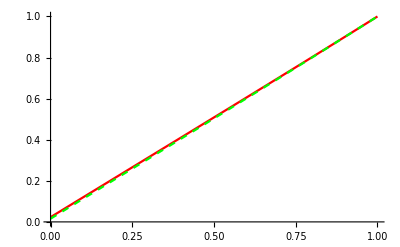

```mathematica
l=b=1;
k=3;
ϕ[x_]=(x-l)^3 (3l^2+4l x+3x^2);
γ[x_]=(x-l)^2 (3l^2+2l x+x^2);
v[x_]= Subscript[c, 1] ϕ[x]+Subscript[c, 2] γ[x];
u[x_]=v[x]+x;
eq[x_]=b u[x]-k x+(2l+x)D[u[x], {x,4}]+2D[u[x], {x,3}]//Expand
sol1=Integrate[eq[x] ϕ[x] , {x,0,l}]
sol2=Integrate[eq[x] γ[x] , {x,0,l}]
ncs=Solve[sol1==0 && sol2==0,{Subscript[c, 1],Subscript[c, 2]}];
nc1=ncs[[1,1,2]]
nc2=ncs[[1,2,2]]
nv[x_]=nc1 ϕ[x]+nc2 γ[x]
nu[x_]=nv[x]+x

(* Exercício anterior *)
v[x_]=a ϕ[x];
u[x_]=v[x]+x;
eq[x_]=b u[x]-k x+(2l+x)D[u[x], {x,4}]+2D[u[x], {x,3}]//Expand;
sol=Integrate[eq[x] ϕ[x], {x,0,l}];
na=Solve[sol==0,a][[1,1,2]];
nvant[x_]=na ϕ[x];
nuant[x_]=nvant[x]+x;

Plot[{nu[x], nuant[x]},{x,0,l},PlotStyle->{Red, {Dashed,Green}}]
```